# Predator Prey System

This notebook shows how to solve a system of 2 ODEs numerically, and draw its solutions. The example chosen is a predator-prey system - which we think her of rabbits and foxes (example in Section 2.1 of BDH).

### Setting up the equations, finding their numerical solution

```mathematica
Clear[R,f, g,  F,t];
f[R_, F_]:=2 R - 1.2 R F;
g[R_, F_]:= -F+0.9 R F;
R0 = 1;
F0 = 0.5;
tinit =0;
tfinal = 20;

sol=NDSolve[{R'[t]==f[R[t],F[t]],F'[t]==g[R[t],F[t]], R[0]==R0, F[0]==F0},{R[t],F[t]},{t,tinit, tfinal}]
```

{{R[t]→InterpolatingFunction[…][t],F[t]→InterpolatingFunction[…][t]}}

### Plotting the solutions vs time

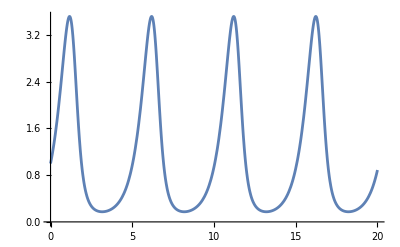

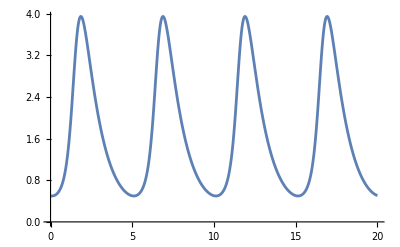

```mathematica
Rplot=Plot[R[t]/.sol, {t, tinit, tfinal}]
Fplot=Plot[F[t]/.sol, {t, tinit, tfinal}]
```

#### Plotting the Rabbits vs time and Foxes vs Time together

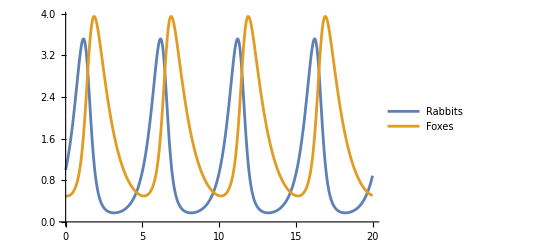

```mathematica
Plot[{R[t]/.sol,F[t]/.sol}, {t, tinit, tfinal},PlotLegends->{"Rabbits", "Foxes"}]
```

### Equilibria

Equilibria occur when (R’, F’)=(0, 0), that is, when neither variables move at these points. We can solve that equation, knowing that R’= f(R, G), F’ = g(R,G) :

{{R→1.11111,F→1.66667},{R→0.,F→0.}}

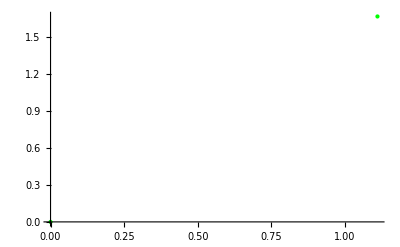

```mathematica
Clear[R, F, f, g];
f[R_, F_]:=2 R - 1.2 R F;
g[R_, F_]:= -F+0.9 R F;
eq=NSolve[{f[R, F]==0,g[R, F]==0}, {R, F}]
eqplot=ListPlot[{R,F}/.eq, PlotStyle->{Green, PointSize[Large]}]
```

### Phase portrait: using parametric plot

As in for the case of a single autonomous ODE,  we can draw the phase portrait representing all the qualitatively different solutions in one drawing. Since there are 2 variables, we must do it in the (R, F)-plane this time. Time becomes a parameter of trajectories, invisible in the plot. I draw 6 solutions here, including the 2 equilibria (in green). How many different ones should you draw to represent all possible qualitatively different solutions? (Hint. 3 of the solutions drawn are qualitatively the same and one solution is missing). Note that I chose tfinal so that some solutions did not close up, to get a sense of the direction of the trajectories.

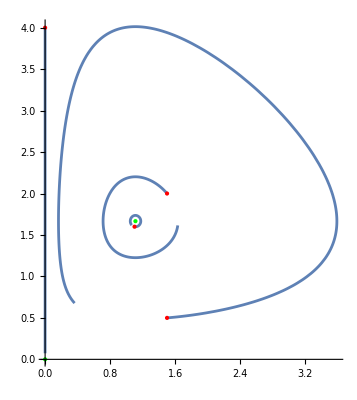

```mathematica
tinit =0;
tfinal = 4;
initpts ={{1.5, 0.5}, {1.5, 2}, {0, 4}, {1.1, 1.6}};
sol=Table[NDSolve[{R'[t]==f[R[t],F[t]],F'[t]==g[R[t],F[t]], R[0]==initpts[[k,1]], F[0]==initpts[[k,2]]},{R,F},{t,tinit, tfinal}], {k, 1, Length[initpts]}];
myplot= Show[Table[ParametricPlot[Evaluate[{R[t], F[t]}/.sol[[k]]], {t, tinit, tfinal}, PlotRange->All, AxesOrigin->{0,0}, AspectRatio->Automatic],{k, 1, Length[initpts]}],
ListPlot[initpts, PlotStyle->{Red, PointSize[Large]}], eqplot]
```

```mathematica
N[10/9]
```

1.11111

## Stream Plot

StreamPlot is a convenient way to get a general sense of the way the solutions trajectories fit together. But this graph is somewhat incomplete. For one thing, it does not show the equilibria.

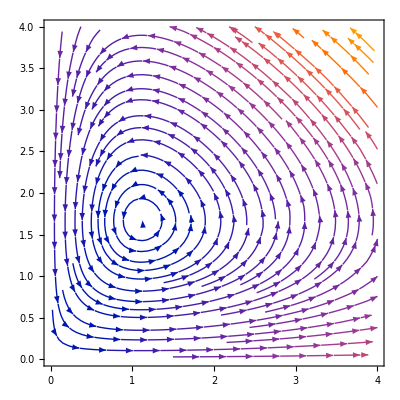

```mathematica
mystreamplot = StreamPlot[{f[R, F], g[R, F]}, {R, 0, 4}, {F, 0, 4}]
```

We can  superimpose the “myplot” we did earlier, to complete the stream plot (but there still is one solution missing that’s qualitatively different from all the other ones!)

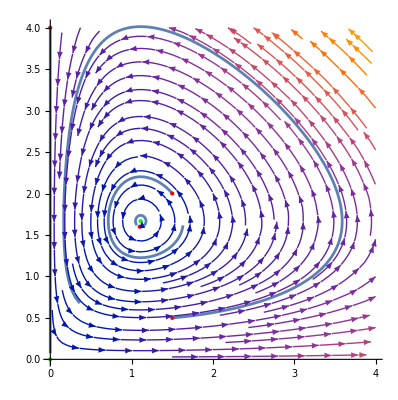

```mathematica
Show[myplot, mystreamplot]
```

If we had to describe this system, we’d say that there are 5 qualitatively different solutions to this system:
1. The (0, 0) equilibrium, representing no rabbits nor foxes. This equilibrium is stable? unstable? because a (any?) nearby solution does ...
2. The (1.111..., 1.6666...) equilibrium, where Rabbits and Foxes coexist.  This equilibrium is stable? unstable? because a  (any?) nearby solution does ...
3. The solution when there are foxes but no rabbits: foxes die out (on the F axis), represented by a downward vertical solution
4. The solution when there are rabbits but no foxes ... what happens to the rabbits?
5.  All the other solutions (most of them) oscillate around the non 0 equilibrium: foxes eat too many rabbits, who die out a bit. But then the foxes die out for lack of food. So the rabbit population rebounds, and the foxes start eating them up too much again ... All these oscillating solutions are qualitatively the same.  They only differ by the amplitude of their oscillations.